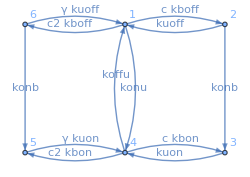

```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica"];
Get["ctmc`"]
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51;
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
τfun[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]:=Evaluate[τ];
τNum[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=Evaluate[τ];
```

```mathematica
(*Joint PDF of ON/OFF durations*)
ClearAll[Pjoint];
ClearAll[d2LogPjoint];
ClearAll[integrand];
ClearAll[expr1];
ClearAll[expr2];
ClearAll[exprS1];
ClearAll[exprS12];

expr1 = FoffOn /.{γ->1};
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Simplify[Apart[exprS1,s2]];
```

```mathematica
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
d2LogPjoint =D[Log[Pjoint],{c,2}];
integrand = Pjoint *d2LogPjoint ;
```

```mathematica
(*Checking that ILT ran correctly*)
PjointSimpl=Simplify[Pjoint,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konu (konb+kuoff)),B==c kbon+c2 kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2}]
```

1/(4 √A √D)ⅇ^(-1/2 (√A+c kboff+c2 kboff+konb+konu+kuoff) t1-1/2 (B+√D) t2) koffu (√A (1+ⅇ^(√A t1)) konu (B-B ⅇ^(√D t2)+√D (1+ⅇ^(√D t2))+2 (-1+ⅇ^(√D t2)) kuon)+(-1+ⅇ^(√A t1)) (-c2 √D kboff konu-c2 √D ⅇ^(√D t2) kboff konu-c √D (1+ⅇ^(√D t2)) kboff konu+√D konb konu+√D ⅇ^(√D t2) konb konu-√D konu^2-√D ⅇ^(√D t2) konu^2+B (-1+ⅇ^(√D t2)) konu (c kboff+c2 kboff-konb+konu-kuoff)+√D konu kuoff+√D ⅇ^(√D t2) konu kuoff-4 c2 kboff konb kuon+4 c2 ⅇ^(√D t2) kboff konb kuon+2 c (-1+ⅇ^(√D t2)) kboff (2 konb-konu) kuon+2 c2 kboff konu kuon-2 c2 ⅇ^(√D t2) kboff konu kuon-2 konb konu kuon+2 ⅇ^(√D t2) konb konu kuon+2 konu^2 kuon-2 ⅇ^(√D t2) konu^2 kuon-2 konu kuoff kuon+2 ⅇ^(√D t2) konu kuoff kuon))

```mathematica
(*Compiling the integrand*)
ClearAll[integrandC];
integrandC=Compile[{{c,_Real},{c2,_Real},{t1,_Real},{t2,_Real},{kboff,_Real},{konb,_Real},{kuon,_Real},{kbon,_Real},{koffu,_Real},{kuoff,_Real},{konu,_Real}},
Evaluate[integrand],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
(*Adding numerical guards*)
ClearAll[integrandCNum];
integrandCNum[c_?NumericQ,c2_?NumericQ,t1_?NumericQ,t2_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=integrandC[N[c],N[c2],N[t1],N[t2],N[kboff],N[konb],N[kuon],N[kbon],N[koffu],N[kuoff],N[konu]];
(*Check*)
(*integrandCNum[__]:=0.;*)
integrandCNum[1,1,1,1,1,1,1,1,1,1,1]
```

0.00346896

```mathematica
(*Numerically integrating for the Fisher info rate*)
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=10.;
cw=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];

integral=-NIntegrate[integrandCNum[c0,cw,t1,t2,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10];
integral*c0^2/τfun[c0,cw,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.00103228

```mathematica
(*Wrapping it into a function*)
ClearAll[FisherFast];
ClearAll[FisherSafe];

FisherFast[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=Module[{τPartialEval,integral},
τPartialEval=τNum[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
integral=-NIntegrate[integrandCNum[c0i,c2i,t1,t2,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->1,
MaxRecursion->10];
integral*c0i^2/τPartialEval];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
(*Check*)
ClearAll[cvals];
cvals=10^Range[-1.,2.,3/38];
kmin =0.0001;
kmax = 5.;
kdl=0.0888;
c0=50.;
ω=5;
cw=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,cw,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.00613933

```mathematica
CloseKernels[];
```

```mathematica
ParallelKernels[]
```

```mathematica
LaunchKernels[13];                       (*ensure you actually have sub-kernels running*)
DistributeDefinitions[integrandC,integrandCNum,FisherFast,FisherSafe,cvals,kmin,kmax,kdl,ω,γ];
```

```mathematica
(*Where to save the data*)
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250505";
experiment="w-5-g-1";
fname = "max-F-vs-c-pid";
```

```mathematica
(*Maximize*)
nhours=7;
nmins=60*nhours;
nseconds=60*nmins/3; (*because we're running 3 params/kernel*)
Now
ParallelDo[
results=Reap[
Catch[
TimeConstrained[
NMaximize[
{FisherSafe[cvals[[i]],ω*cvals[[i]],γ,kboff,kmax,kmax,kbon,kmax,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=kmax,
kmin<=konu<=kmax},
{kboff,kbon,kuoff,konu},
Method->"NelderMead",
PrecisionGoal->3,AccuracyGoal->20,MaxIterations->7,
StepMonitor:>Print["Rates = ",{kboff,kbon,kuoff,konu}],
EvaluationMonitor:>Sow[{FisherSafe[cvals[[i]],ω*cvals[[i]],γ,kboff,kmax,kmax,kbon,kmax,kuoff,konu],{kboff,kbon,kuoff,konu}}]
],nseconds,Throw[{"timeout"},$tag]
],$tag
]
];
Save[FileNameJoin[{$HomeDirectory},datadir, date,experiment, fname<>ToString[i]<>".wl"],results]
,{i,1,39},
Method->"CoarsestGrained"
];
Now
```

Mon 5 May 2025 03:12:40GMT+2

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.00270204,0.0831153,2.24634,3.54608}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.00270204,0.0831153,2.24634,3.54608}

Rates = {0.0751719,0.0846043,4.15244,0.0613998}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0157547,0.0486484,2.5438,3.50023}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0285196,0.085994,4.97287,0.0876131}

Rates = {0.006002,0.0483451,2.74028,4.74099}

Rates = {0.006002,0.0483451,2.74028,4.74099}

Rates = {0.0533773,0.0803099,4.28073,0.0876131}

Rates = {0.0533773,0.0803099,4.28073,0.0876131}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

«3 more identical outputs»

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

«1 more identical outputs»

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

«1 more identical outputs»

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.006002,0.00820469,2.67631,0.0782055}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0327302,0.071764,4.89155,0.0688596}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.006002,0.00820469,2.67631,0.0782055}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

«1 more identical outputs»

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0311478,0.086315,3.14382,2.91127}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0311478,0.086315,3.14382,2.91127}

Rates = {0.0311478,0.086315,3.14382,2.91127}

Rates = {0.0144513,0.0643524,1.84363,4.32362}

Rates = {0.0201771,0.0826812,2.50325,4.99252}

Rates = {0.0113345,0.0589791,2.74021,4.74292}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0124413,0.0557096,2.73787,4.80269}

Rates = {0.00834358,0.0222375,2.6762,0.0764638}

Rates = {0.00884109,0.0200797,2.67541,0.0639135}

Rates = {0.00884109,0.0200797,2.67541,0.0639135}

Rates = {0.00996074,0.0576575,2.73704,4.8246}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0888,0.0874194,4.85223,0.0001}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0148675,0.0211447,2.13252,2.6655}

Rates = {0.0105243,0.0601215,2.73648,4.83986}

Rates = {0.0148675,0.0211447,2.13252,2.6655}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

Rates = {0.0128499,0.0595779,2.73455,4.8922}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0888,0.0888,4.85199,0.0001}

Rates = {0.0152807,0.085103,2.50297,5.}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

«3 more identical outputs»

Rates = {0.0888,0.0888,4.85199,0.0001}

Rates = {0.085595,0.0888,4.85143,0.0001}

Rates = {0.0888,0.0877602,4.2854,0.0001}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0151041,0.0838768,2.50294,5.}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0113106,0.0565067,2.73373,4.91521}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0311478,0.086315,3.14382,2.91127}

Rates = {0.0311478,0.086315,3.14382,2.91127}

Rates = {0.014193,0.053046,1.84363,4.32362}

Rates = {0.014193,0.053046,1.84363,4.32362}

Rates = {0.00553729,0.0806882,0.027227,4.91249}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0856429,0.0888,4.85061,0.0001}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

Rates = {0.0888,0.0849069,4.28537,0.0001}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0888,0.0886981,4.28649,0.0001}

Rates = {0.0102661,0.0684408,0.0269517,4.91353}

Rates = {0.0888,0.0849412,4.28535,0.0001}

Rates = {0.0888,0.0888,4.85289,0.0001}

Rates = {0.0484199,0.0881704,4.27669,0.0001}

Rates = {0.0888,0.0849454,4.28534,0.0001}

Rates = {0.0481331,0.0888,4.27661,0.0001}

Rates = {0.0888,0.0849465,4.28534,0.0001}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

«2 more identical outputs»

Rates = {0.0406685,0.0846043,4.9387,0.0915516}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.00980971,0.0650758,0.00148839,5.}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0101986,0.0686485,0.000971821,4.99999}

Rates = {0.0888,0.0888,4.28553,0.0001}

Rates = {0.0134611,0.0577756,2.73073,5.}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0888,0.0884475,4.28727,0.0317364}

Rates = {0.00679149,0.0394681,2.17932,3.87558}

Rates = {0.00679149,0.0394681,2.17932,3.87558}

Rates = {0.0108912,0.0359053,3.05589,4.6059}

Rates = {0.0108912,0.0359053,3.05589,4.6059}

Rates = {0.0888,0.0877657,4.28539,0.0001}

Rates = {0.042847,0.088313,4.93544,0.000138574}

Rates = {0.0888,0.0877671,4.28539,0.0001}

Rates = {0.0427984,0.0883973,4.93543,0.0001}

Rates = {0.0101695,0.0683694,0.000684067,5.}

Rates = {0.0649665,0.0704435,2.74862,4.96476}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0720301,0.0888,4.85252,0.0001}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0406685,0.0846043,4.9387,0.0915516}

Rates = {0.0100868,0.0483742,3.05568,4.61143}

Rates = {0.0888,0.0877674,4.28539,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0457264,0.0765267,4.59214,0.044309}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 7 iterations.

Rates = {0.0888,0.0888,4.28576,0.0001}

Rates = {0.00986966,0.0491264,3.05567,4.61171}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0302196,0.0209315,4.93601,0.969713}

Rates = {0.0888,0.0888,4.28575,0.0001}

Rates = {0.00679149,0.0394681,2.17932,3.87558}

Rates = {0.00679149,0.0394681,2.17932,3.87558}

Rates = {0.00679149,0.0394681,2.17932,3.87558}

«1 more identical outputs»

Rates = {0.0888,0.0888,4.28575,0.0001}

Rates = {0.0888,0.0888,4.85286,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0888,0.0888,4.85286,0.0001}

Rates = {0.00887679,0.0413006,2.1792,3.87654}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0888,0.0888,4.28552,0.0001}

Rates = {0.0089536,0.0403722,2.17814,3.88571}

Rates = {0.0888,0.0888,4.28552,0.0001}

Rates = {0.00834389,0.0406467,2.17676,3.89783}

Rates = {0.0888,0.0888,4.28552,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0087863,0.0414418,2.17656,3.89956}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0882224,0.0858157,4.8525,0.000305089}

Rates = {0.0888,0.0888,4.28523,0.0001}

Rates = {0.0888,0.0888,4.85227,0.0001}

Rates = {0.0888,0.0888,4.85227,0.0001}

Rates = {0.0720252,0.0888,4.85251,0.0001}

Rates = {0.0888,0.0888,4.28603,0.0001}

Rates = {0.072024,0.0888,4.85251,0.0001}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0802746,0.0806882,4.85435,0.027227}

Rates = {0.0675098,0.082701,4.92443,0.0381098}

Rates = {0.0888,0.0888,4.28527,0.0001}

Rates = {0.0606054,0.0888,4.92181,0.0001}

Rates = {0.0888,0.0888,4.28522,0.0001}

Rates = {0.0888,0.0888,4.28521,0.0001}

Rates = {0.0888,0.0888,4.28521,0.0001}

Rates = {0.0888,0.0887004,4.28648,0.0001}

Rates = {0.0888,0.0888,4.28526,0.0001}

Rates = {0.0606079,0.0888,4.9218,0.0001}

Rates = {0.0888,0.0888,4.28526,0.0001}

Rates = {0.0888,0.0887014,4.28648,0.0001}

Rates = {0.0888,0.0888,4.28526,0.0001}

Rates = {0.0578754,0.0632242,3.4971,1.74941}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

«1 more identical outputs»

Rates = {0.0888,0.0887015,4.28648,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0888,0.0865941,4.94948,0.000811112}

Rates = {0.0888,0.0881053,4.28736,0.0329316}

Rates = {0.0888,0.0887971,4.28641,0.0001}

Rates = {0.0888,0.0887983,4.28641,0.0001}

Rates = {0.0888,0.0888,4.28601,0.0001}

Rates = {0.0888,0.0887986,4.28641,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0888,0.0888,4.28266,0.0001}

Rates = {0.0888,0.0888,4.28266,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0888,0.0888,4.28623,0.0001}

Rates = {0.0888,0.0888,4.28588,0.0001}

Rates = {0.0888,0.0888,4.28585,0.0001}

Rates = {0.0888,0.0888,4.28585,0.0001}

Rates = {0.0888,0.0888,4.28585,0.0001}

Rates = {0.0888,0.0888,4.28621,0.0001}

Rates = {0.0888,0.0888,4.28593,0.0001}

Rates = {0.0888,0.0888,4.28593,0.0001}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

«3 more identical outputs»

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0880395,0.0314791,4.93878,1.64167}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

Rates = {0.0831153,0.0883986,4.94959,0.512613}

«3 more identical outputs»

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.087408,0.0646632,4.92074,0.0467645}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0881366,0.0620435,4.9527,0.0613998}

Rates = {0.0888,0.0886105,4.28651,0.0001}

Rates = {0.0888,0.0886118,4.28651,0.0001}

Rates = {0.0888,0.0886327,4.2864,0.0001}

Mon 5 May 2025 10:12:40GMT+2

```mathematica
(*Plot*)
ClearAll[fname];
ClearAll[experiment];
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250505";
experiment="w-5-g-1";
fname = "max-F-vs-c-pid";
nparams=39;
(*datafile = FileNameJoin[{$HomeDirectory},datadir,date,experiment, fname<>ToString[2]<>".wl"];
results = Get[datafile];*)
ClearAll[results];
resultsClean=Table[
datafile = FileNameJoin[{$HomeDirectory},datadir,date,experiment, fname<>ToString[i]<>".wl"];
results = Get[datafile];
If[results[[1]][[1]]=="timeout",Print["timeout"<>ToString[1]];results[[2]][[1]][[1]][[1]],results[[1]][[1]]]
,{i,1,nparams}
];
```

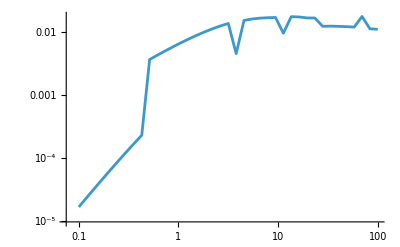

```mathematica
ListLinePlot[Table[{cvals[[i]],resultsClean[[i]]},{i,1,nparams}],ScalingFunctions->{"Log","Log"}]
```

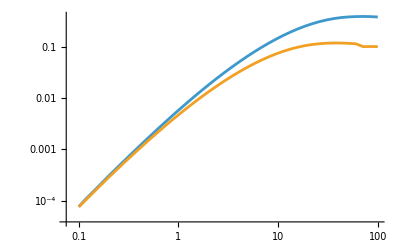

```mathematica
ListLinePlot[{Table[{cvals[[i]],results01[[i]][[1]][[1]]},{i,1,42}],Table[{cvals[[i]],results1[[i]][[1]][[1]]},{i,1,42}]},
ScalingFunctions->{"Log","Log"}]
```